# Augmented Truncated Cube

### Author

Eric W. Weisstein
October 23, 2024

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/AugmentedTruncatedCube.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/AugmentedTruncatedCube.html.

©2024 Wolfram Research, Inc. except for portions noted otherwise

## Graphics

### Solid, net, and skeleton

```mathematica
With[{pname="AugmentedTruncatedCube"},
GraphicsRow[Show[#,ImageSize->{Automatic,250}]&/@{
Graphics3D[{Opacity[.8],PolyhedronData[pname,"Polyhedron"]},Method->{"ShrinkWrap"->True},Boxed->False],
GraphData[pname<>"Graph"]//StyleGraphs,
PolyhedronData[pname,"Net"]
}]
]
```

-Graphics-

### Solid

```mathematica
PolyhedronData["AugmentedTruncatedCube","Orientations"]
```

Missing[NotAvailable]

```mathematica
PolyhedronData["AugmentedTruncatedCube"]
```

-Graphics3D-

### Net

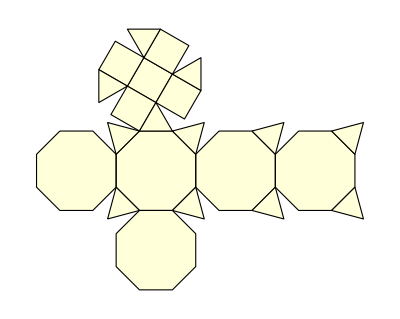

```mathematica
PolyhedronData["AugmentedTruncatedCube","Net"]
```

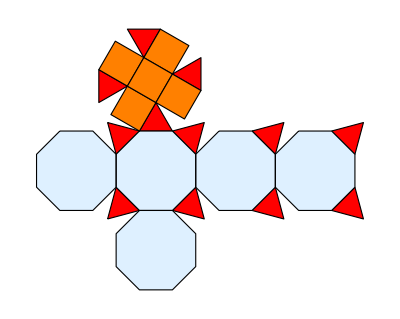

```mathematica
PolyhedronData["AugmentedTruncatedCube","Net","Colored"]
```

```mathematica
NetPrintout[PolyhedronData["AugmentedTruncatedCube","Polyhedron"],"SmallTriakisOctahedron.pdf"]
```

## Properties

```mathematica
<<MathWorld`PolyhedronOperations`
```

```mathematica
p=PolyhedronData[pname="AugmentedTruncatedCube","Polyhedron"]
```

Polyhedron[…]

### Centroid

```mathematica
Graphics3D[{AbsolutePointSize[10],
Point[{0,0,0}],{Blue,Point[PolyhedronData[pname,"Centroid"]]},Opacity[.2],PolyhedronData[pname,"GraphicsComplex"]}]
```

-Graphics3D-

```mathematica
PolyhedronData[pname,"Centroid"]
```

{0,0,1/64 (9+2 √2)}

```mathematica
RegionCentroid[p]//FullSimplify
```

{0,0,1/64 (9+2 √2)}

```mathematica
PolyhedronCentroid[p]
```

{0,0,1/64 (9+2 √2)}

### Circumsphere

```mathematica
PolyhedronData[pname,"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Circumsphere[p]
```

Circumsphere::indep: Circumsphere does not exist for Polyhedron[{{-1/2,1/2 (1+√2),1/2 (-1-√2)},{-1/2,1/2 (1+√2),1/2 (1+√2)},{-1/2,1/2 (-1-√2),1/2 (-1-√2)},{-1/2,1/2 (-1-√2),1/2 (1+√2)},{0,-1/(√2),1/2 (1+2 √2)},{0,1/(√2),1/2 (1+2 √2)},{1/2,1/2 (1+√2),1/2 (-1-√2)},{1/2,1/2 (1+√2),1/2 (1+√2)},{1/2,1/2 (-1-√2),1/2 (-1-√2)},{1/2,1/2 (-1-√2),1/2 (1+√2)},«18»},{{7,15,13,9,3,21,23,1},{9,19,20,10,4,28,27,3},«7»,{20,14,10},«12»}].

Circumsphere[Polyhedron[…]]

```mathematica
sphere=MyCircumsphere[p]
```

{}

### Convex

```mathematica
ConvexPolyhedronQ[p]
```

True

### DihedralAngles

```mathematica
PolyhedronData[pname,"DihedralAngles"]//Tally
```

{{π/2,8},{ArcCos[-1/(√3)],20},{ArcCos[-√(2/3)],12},{ArcCos[(-2-√2)/(2 √3)],4},{(3 π)/4,4}}

```mathematica
DihedralAngles[p]//FullSimplify//Tally
```

{{π/2,8},{ArcSec[-√3],20},{ArcCos[-√(2/3)],12},{ArcCos[-(2+√2)/(2 √3)],4},{(3 π)/4,4}}

### EdgeLengths

```mathematica
PolyhedronData[pname,"EdgeLengths"]
```

{1}

```mathematica
PolyhedronData[pname,"Lines"]/.Line[l_]:>EuclideanDistance@@l//FullSimplify//Union
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (-1-√2)+1/2 (1+√2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{1}

### Faces

### GeneralizedDiameter

```mathematica
PolyhedronData[pname,"GeneralizedDiameter"]
```

2 √(2+√2)

```mathematica
GeneralizedDiameter[p]//FullSimplify//Quiet
```

2 √(2+√2)

### Insphere

```mathematica
PolyhedronData[pname,"Insphere"]
```

Missing[NotApplicable]

```mathematica
Insphere[p]
```

Insphere::indep: Insphere does not exist for Polyhedron[{{-1/2,1/2 (1+√2),1/2 (-1-√2)},{-1/2,1/2 (1+√2),1/2 (1+√2)},{-1/2,1/2 (-1-√2),1/2 (-1-√2)},{-1/2,1/2 (-1-√2),1/2 (1+√2)},{0,-1/(√2),1/2 (1+2 √2)},{0,1/(√2),1/2 (1+2 √2)},{1/2,1/2 (1+√2),1/2 (-1-√2)},{1/2,1/2 (1+√2),1/2 (1+√2)},{1/2,1/2 (-1-√2),1/2 (-1-√2)},{1/2,1/2 (-1-√2),1/2 (1+√2)},«18»},{{7,15,13,9,3,21,23,1},{9,19,20,10,4,28,27,3},«7»,{20,14,10},«12»}].

Insphere[Polyhedron[…]]

```mathematica
MyInsphere[p]
```

{}

### InertiaTensor

```mathematica
PolyhedronData[pname,"InertiaTensor"]
```

{{1/320 (163+139 √2),0,0},{0,1/320 (163+139 √2),0},{0,0,1/160 (74+47 √2)}}

```mathematica
MomentOfInertia[p,{0,0,0}]/Volume[p]//RootReduce//Timing
```

{1.78774,{{1/320 (163+139 √2),0,0},{0,1/320 (163+139 √2),0},{0,0,1/160 (74+47 √2)}}}

```mathematica
PolyhedronInertiaTensor[p]//Timing
```

### MeanCylindricalRadius

```mathematica
NIntegrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.87475

```mathematica
(i=Integrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanCylindricalSquareRadius

```mathematica
NIntegrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

0.877925

```mathematica
(i=Integrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{0.188693,1/160 (74+47 √2)}

```mathematica
N[i]
```

0.877925

### MeanSphericalRadius

```mathematica
NIntegrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

1.20093

```mathematica
(i=Integrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanSphericalSquareRadius

```mathematica
NIntegrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

1.56264

```mathematica
(i=Integrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{0.196707,3/320 (79+62 √2)}

```mathematica
N[i]
```

1.56264

### Midsphere

```mathematica
PolyhedronData[pname,"Midsphere"]
```

Missing[NotApplicable]

```mathematica
Midsphere[p]
```

{}

### SurfaceArea

```mathematica
PolyhedronData[pname,"SurfaceArea"]
```

15+10 √2+3 √3

```mathematica
SurfaceArea[p]//FullSimplify
```

15+10 √2+3 √3

```mathematica
Total[Area/@PolyhedronData[pname,"Polygons"]]//FullSimplify
```

15+10 √2+3 √3

### VertexSubsetHulls

```mathematica
PolyhedronData[pname,"VertexSubsetHulls"]
```

{AugmentedTruncatedCube→{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}},SquareCupola→{{2,4,5,6,8,10,11,12,14,16,22,24}},TruncatedCube→{{1,2,3,4,7,8,9,10,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}}}

#### Platonic

```mathematica
(h=VertexSubsetHulls[p,"Platonic","Skip"->{}])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

Finding icosahedra by building up from equilateral triangles...

{0.09435,{}}

### Volume

```mathematica
PolyhedronData[pname,"Volume"]
```

8+(16 √2)/3

```mathematica
Volume[p]//FullSimplify
```

8+(16 √2)/3

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

8+(16 √2)/3

## Perspective projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["Cuboctahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### XXX

```mathematica
PolyhedronProjectionGraph[PolyhedronData["DuererSolid","Polyhedron"],]
```